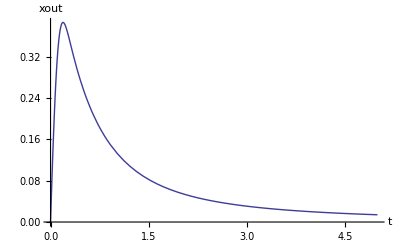

```mathematica
a=0.75;
x0=0 ;
Vin = Sqrt[50/Pi]*Exp[-50*t^2];
DESolve =NDSolve [{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
 x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
 x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
 x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
 x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
 x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
 x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
 x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
 x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
 x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
 x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
 x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
 x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
 x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
 x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
 x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
 x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
 x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
 x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
 x20'[t]==x19[t]-(1+a)*x20[t]+Vin, 
x1[0] ==0, x2[0]==0, x3[0] ==0, x4[0]==0, x5[0]==0, x6[0] ==0, x7[0]==0, x8[0] ==0, x9[0]==0, x10[0] ==0, 
x11[0] ==0, x12[0]==0, x13[0] ==0, x14[0]==0, x15[0]==0, x16[0] ==0, x17[0]==0, x18[0] ==0, x19[0]==0, x20[0] ==0}, 
{x1[t] , x2[t], x3[t], x4[t], x5[t], x6[t], x7[t], x8[t], x9[t], x10[t],
x11[t] , x12[t], x13[t], x14[t], x15[t], x16[t], x17[t], x18[t], x19[t], x20[t]},{t, 0,200}];

{x1out[t_], x2out[t_], x3out[t_], x4out[t_], x5out[t_], x6out[t_], x7out[t_], x8out[t_], x9out[t_], x10out[t_], x11out[t_], x12out[t_], x13out[t_], x14out[t_],x15out[t_], x16out[t_], x17out[t_], x18out[t_],  x19out[t_], x20out[t_]}={x1[t], x2[t],  x3[t], x4[t],x5[t], x6[t],x7[t], x8[t],x9[t], x10[t],x11[t], x12[t],x13[t], x14[t],x15[t], x16[t],x17[t], x18[t],x19[t], x20[t]}/.Flatten[DESolve];

Plot[x20out[t], {t,0,5},AxesLabel->{"t","xout"}]
```

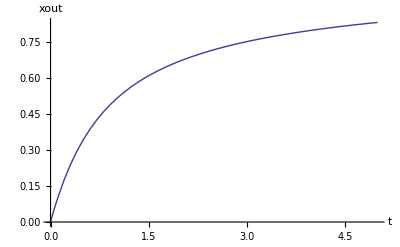

```mathematica
a=0.75;
x0=0 ;
Vin = UnitStep[t];
DESolve =NDSolve [{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
 x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
 x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
 x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
 x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
 x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
 x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
 x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
 x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
 x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
 x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
 x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
 x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
 x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
 x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
 x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
 x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
 x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
 x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
 x20'[t]==x19[t]-(1+a)*x20[t]+Vin, 
x1[0] ==0, x2[0]==0, x3[0] ==0, x4[0]==0, x5[0]==0, x6[0] ==0, x7[0]==0, x8[0] ==0, x9[0]==0, x10[0] ==0, 
x11[0] ==0, x12[0]==0, x13[0] ==0, x14[0]==0, x15[0]==0, x16[0] ==0, x17[0]==0, x18[0] ==0, x19[0]==0, x20[0] ==0}, 
{x1[t] , x2[t], x3[t], x4[t], x5[t], x6[t], x7[t], x8[t], x9[t], x10[t],
x11[t] , x12[t], x13[t], x14[t], x15[t], x16[t], x17[t], x18[t], x19[t], x20[t]},{t, 0,200}];

{x1out[t_], x2out[t_], x3out[t_], x4out[t_], x5out[t_], x6out[t_], x7out[t_], x8out[t_], x9out[t_], x10out[t_], x11out[t_], x12out[t_], x13out[t_], x14out[t_],x15out[t_], x16out[t_], x17out[t_], x18out[t_],  x19out[t_], x20out[t_]}={x1[t], x2[t],  x3[t], x4[t],x5[t], x6[t],x7[t], x8[t],x9[t], x10[t],x11[t], x12[t],x13[t], x14[t],x15[t], x16[t],x17[t], x18[t],x19[t], x20[t]}/.Flatten[DESolve];

Plot[x20out[t], {t,0,5},AxesLabel->{"t","xout"}]
```